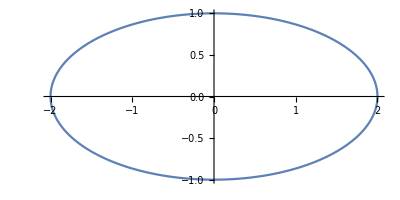

-Graphics3D-

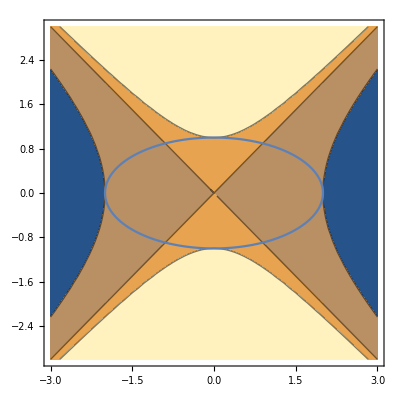

```mathematica
g1=Plot3D[{y^2-x^2},{x,-3,3},{y,-3,3},PlotStyle->Directive[Orange,Specularity[White,50],Opacity[0.5]]];
g2=ParametricPlot3D[{2*Cos[u],Sin[u],t},{u,0,2*Pi},{t,-6,6},PlotStyle->Directive[Green,Specularity[White,50],Opacity[0.8]]];
g3=ContourPlot[{y^2-x^2},{x,-3,3},{y,-3,3},Contours->{-4,0,1}];
g4=ParametricPlot[{2*Cos[u],Sin[u]},{u,0,2*Pi}]
Show[g1,g2]
Show[g3,g4]
```

-Graphics3D-

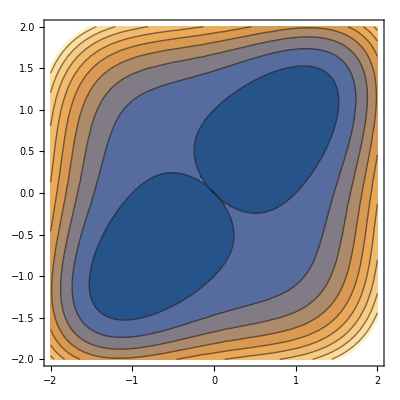

```mathematica
Plot3D[{y^4+x^4-x^2-2x*y-y^2},{x,-2,2},{y,-2,2},PlotStyle->Directive[Orange,Specularity[White,50],Opacity[0.5]]]
ContourPlot[{y^4+x^4-x^2-2x*y-y^2},{x,-2,2},{y,-2,2}]
```

```mathematica
ParametricPlot3D[{Cos[u],Sin[u],t},{u,0,2*Pi},{t,-3,3},PlotStyle->Directive[Green,Specularity[White,50],Opacity[0.8]]]
```

-Graphics3D-

```mathematica
Plot3D[Sqrt[1-x^2-y^2],{x,-1,1},{y,-1,1},Filling->Bottom,Ticks->None,BoundaryStyle->Black,AxesLabel->{x,y,z},PlotStyle->Opacity[1]]
```

-Graphics3D-

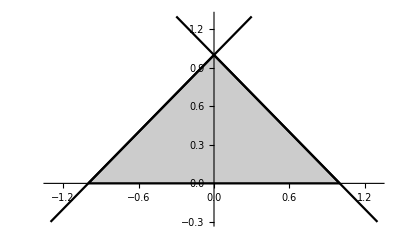

```mathematica
f[x_]:=1-x;g[x_]:=1+x;
Quxian1=Plot[f[x],{x,-0.3,1.3},AxesStyle->Arrowheads[0.04],PlotStyle->Black];
Quxian2=Plot[g[x],{x,-1.3,0.3},AxesStyle->Arrowheads[0.04],PlotStyle->Black];
Quyu1=Plot[{0,f[x]},{x,0,1},Filling->{1->{2}},PlotRange->All,AxesStyle->Arrowheads[0.04],PlotStyle->Black];
Quyu2=Plot[{0,g[x]},{x,-1,0},Filling->{1->{2}},PlotRange->All,AxesStyle->Arrowheads[0.04],PlotStyle->Black];
Show[Quyu1,Quyu2,Quxian1,Quxian2]
```

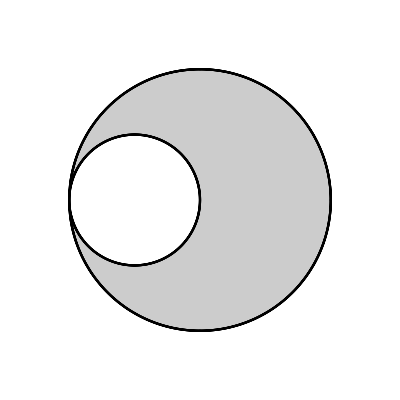

```mathematica
Quxian1=PolarPlot[2Cos[t],{t,0,2Pi},PlotStyle->Black,Ticks->{{-2,-1,0,1,2},{-2,-1,0,1,2}}];
Quxian2=PolarPlot[4Cos[t],{t,0,2Pi},PlotStyle->Black,Ticks->{{-2,-1,0,1,2},{-2,-1,0,1,2}}];
Quyu=RegionPlot[(x-1)^2+y^2>=1&&(x-2)^2+y^2<=4,{x,-1,5},{y,-3,3},PlotStyle->GrayLevel[.8],BoundaryStyle->Black,Ticks->{{-2,-1,0,1,2},{-2,-1,0,1,2}},PlotPoints->100];
Show[Quyu,Quxian1,Quxian2,PlotRange->{{-0.5,4.5},{-2.5,2.5}},AxesStyle->Arrowheads[0.04],Axes->Automatic,AspectRatio->1,Frame->False,Ticks->{{-2,-1,0,1,2},{-2,-1,0,1,2}}]
```

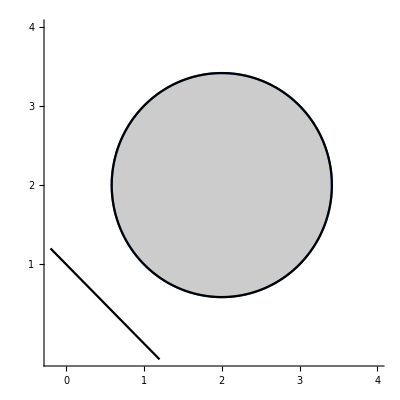

```mathematica
C1=ParametricPlot[{Sqrt[2]Cos[t]+2,Sqrt[2]Sin[t]+2},{t,0,2Pi},PlotStyle->Black];
C2=RegionPlot[(x-2)^2+(y-2)^2≤2,{x,0,4},{y,0,4},PlotStyle->GrayLevel[.8],AxesStyle->Arrowheads[0.04],Axes->Automatic,AspectRatio->1,Frame->False,PlotRange->{{-0.2,4},{-0.2,4}},Ticks->{{0,1,2,3,4},{1,2,3,4}}];
L=Plot[1-x,{x,-0.2,1.2},PlotStyle->Black,AxesStyle->Arrowheads[0.04],Axes->Automatic,AspectRatio->1,Frame->False];
Show[C2,C1,L]
```

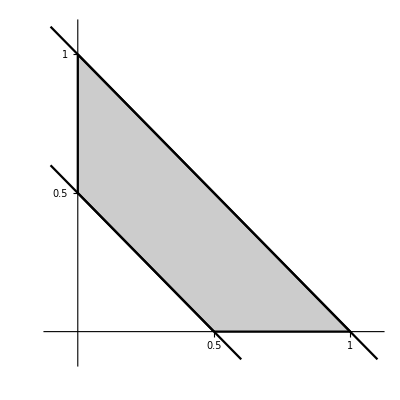

```mathematica
f[x_]:=1-x;g[x_]:=1/2-x;
Quxian1=Plot[f[x],{x,-0.1,1.1},AxesStyle->Arrowheads[0.04],PlotStyle->Black,AspectRatio->1,Ticks->{{0.5,1},{0.5,1}}];
Quxian2=Plot[g[x],{x,-0.1,0.6},AxesStyle->Arrowheads[0.04],PlotStyle->Black,AspectRatio->1,Ticks->{{0.5,1},{0.5,1}}];
Quyu1=Plot[{g[x],f[x]},{x,0,0.5},Filling->{1->{2}},PlotRange->All,AxesStyle->Arrowheads[0.04],PlotStyle->Black,AspectRatio->1,Ticks->{{0.5,1},{0.5,1}}];
Quyu2=Plot[{0,f[x]},{x,0.5,1},Filling->{1->{2}},PlotRange->All,AxesStyle->Arrowheads[0.04],PlotStyle->Black,AspectRatio->1];
LX0=ParametricPlot[{0,y},{y,0.5,1},PlotStyle->Black,PlotStyle->Black];
Show[Quyu1,Quyu2,Quxian1,Quxian2,LX0]
```

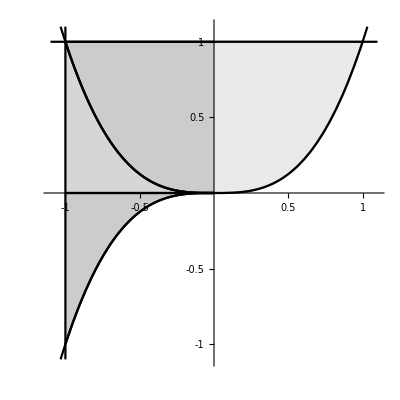

```mathematica
f[x_]:=x^3;g[x_]:=1;h[x_]:=-x^3;
Quxian1=Plot[f[x],{x,-CubeRoot[1.1],CubeRoot[1.1]},AxesStyle->Arrowheads[0.04],PlotStyle->Black,AspectRatio->1,Ticks->{{0.5,1},{0.5,1}}];
Quxian2=Plot[g[x],{x,-1.1,1.1},AxesStyle->Arrowheads[0.04],PlotStyle->Black,AspectRatio->1,Ticks->{{0.5,1},{0.5,1}}];
Quxian3=Plot[h[x],{x,-CubeRoot[1.1],0},AxesStyle->Arrowheads[0.04],PlotStyle->Black,AspectRatio->1,Ticks->{{0.5,1},{0.5,1}}];
Quyu1=Plot[{f[x],g[x]},{x,0,1},Filling->{1->{2}},PlotRange->All,AxesStyle->Arrowheads[0.04],AspectRatio->1,PlotStyle->GrayLevel[0.6],Ticks->{{-1,-0.5,0.5,1},{-1,-0.5,0.5,1}}];
Quyu2=Plot[{h[x],g[x]},{x,-1.0,0.0},Filling->{1->{2}},PlotRange->All,AxesStyle->Arrowheads[0.04],PlotStyle->Black,AspectRatio->1,PlotStyle->GrayLevel[.4]];
Quyu3=Plot[{h[x],y=0},{x,-1.0,0.0},Filling->{1->{2}},PlotRange->All,AxesStyle->Arrowheads[0.04],AspectRatio->1,PlotStyle->GrayLevel[.2]];
Quyu4=Plot[{f[x],y=0},{x,-1.0,0.0},Filling->{1->{2}},PlotRange->All,AxesStyle->Arrowheads[0.04],AspectRatio->1,PlotStyle->GrayLevel[0]];
LX0=ParametricPlot[{-1,y},{y,-1.1,1.1},PlotStyle->Black,PlotStyle->Black];
Show[Quyu1,Quyu2,Quyu3,Quyu4,Quxian1,Quxian2,Quxian3,LX0]
```

```mathematica
Integrate[u*Sin[1/u],u]
```

1/2 u Cos[1/u]+1/2 u^2 Sin[1/u]+1/2 SinIntegral[1/u]

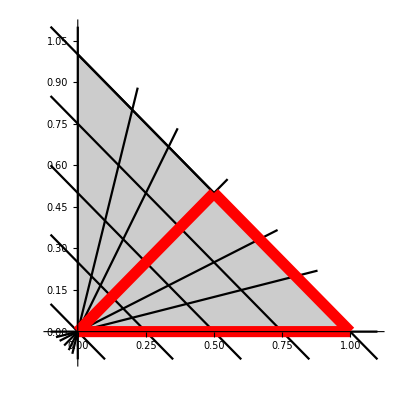

```mathematica
f[b_,x_]:=b-x;g[k_,x_]:=k*x;
Quxian11=Plot[f[1,x],{x,-0.1,1.1},AxesStyle->Arrowheads[0.04],PlotStyle->Black,AspectRatio->1];
Quxian12=Plot[f[0.75,x],{x,-0.1,0.85},AxesStyle->Arrowheads[0.04],PlotStyle->Black,AspectRatio->1];
Quxian13=Plot[f[0.50,x],{x,-0.1,0.60},AxesStyle->Arrowheads[0.04],PlotStyle->Black,AspectRatio->1];
Quxian14=Plot[f[0.25,x],{x,-0.1,0.35},AxesStyle->Arrowheads[0.04],PlotStyle->Black,AspectRatio->1];
Quxian15=Plot[f[0.0,x],{x,-0.1,0.1},AxesStyle->Arrowheads[0.04],PlotStyle->Black,AspectRatio->1];
Quxian20=Plot[{g[0,x]},{x,-0.1,1.1},AxesStyle->Arrowheads[0.04],PlotStyle->Black,AspectRatio->1];
Quxian21=Plot[{g[1/4,x]},{x,-0.4/5,4.4/5},AxesStyle->Arrowheads[0.04],PlotStyle->Black,AspectRatio->1];
Quxian22=Plot[{g[1/2,x]},{x,-0.2/3,2.2/3},AxesStyle->Arrowheads[0.04],PlotStyle->Black,AspectRatio->1];
Quxian23=Plot[{g[1,x]},{x,-0.1/2,1.1/2},AxesStyle->Arrowheads[0.04],PlotStyle->Black,AspectRatio->1];
Quxian24=Plot[{g[2,x]},{x,-0.1/3,1.1/3},AxesStyle->Arrowheads[0.04],PlotStyle->Black,AspectRatio->1];
Quxian25=Plot[{g[4,x]},{x,-0.1/5,1.1/5},AxesStyle->Arrowheads[0.04],PlotStyle->Black,AspectRatio->1];
Quxian26=ParametricPlot[{0,y},{y,-0.1,1.1},AxesStyle->Arrowheads[0.04],PlotStyle->Black,AspectRatio->1];
Quxian31=Plot[{f[1,x]},{x,0.5,1},AxesStyle->Arrowheads[0.04],PlotStyle->{Red,Thickness[0.02]},AspectRatio->1];
Quxian32=Plot[{g[1,x]},{x,0,0.5},AxesStyle->Arrowheads[0.04],PlotStyle->{Red,Thickness[0.02]},AspectRatio->1];
Quxian33=Plot[{g[0,x]},{x,0,1},AxesStyle->Arrowheads[0.04],PlotStyle->{Red,Thickness[0.02]},AspectRatio->1];
Quyu1=Plot[f[1,x],{x,0,1},Filling->Bottom,PlotRange->All,AxesStyle->Arrowheads[0.04],PlotStyle->Black,AspectRatio->1];
Show[Quyu1,Quxian11,Quxian12,Quxian13,Quxian14,Quxian15,Quxian20,Quxian21,Quxian22,Quxian23,Quxian24,Quxian25,Quxian26,Quxian31,Quxian32,Quxian33]
```

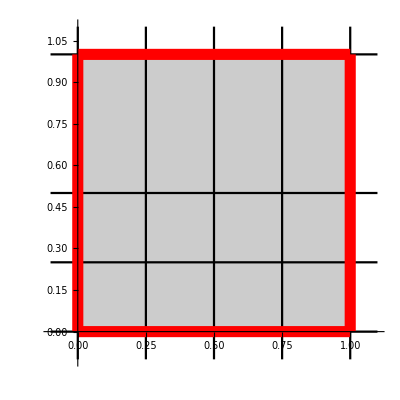

```mathematica
f[b_]:=b;g[k_]:=k;
Quxian11=ParametricPlot[{f[1],y},{y,-0.1,1.1},AxesStyle->Arrowheads[0.04],PlotStyle->Black,AspectRatio->1];
Quxian12=ParametricPlot[{f[0.75],y},{y,-0.1,1.1},AxesStyle->Arrowheads[0.04],PlotStyle->Black,AspectRatio->1];
Quxian13=ParametricPlot[{f[0.5],y},{y,-0.1,1.1},AxesStyle->Arrowheads[0.04],PlotStyle->Black,AspectRatio->1];
Quxian14=ParametricPlot[{f[0.25],y},{y,-0.1,1.1},AxesStyle->Arrowheads[0.04],PlotStyle->Black,AspectRatio->1];
Quxian15=ParametricPlot[{f[0.0],y},{y,-0.1,1.1},AxesStyle->Arrowheads[0.04],PlotStyle->Black,AspectRatio->1];
Quxian20=Plot[{g[0]},{x,-0.1,1.1},AxesStyle->Arrowheads[0.04],PlotStyle->Black,AspectRatio->1];
Quxian21=Plot[{g[1/4]},{x,-0.1,1.1},AxesStyle->Arrowheads[0.04],PlotStyle->Black,AspectRatio->1];
Quxian22=Plot[{g[1/2]},{x,-0.1,1.1},AxesStyle->Arrowheads[0.04],PlotStyle->Black,AspectRatio->1];
Quxian23=Plot[{g[1]},{x,-0.1,1.1},AxesStyle->Arrowheads[0.04],PlotStyle->Black,AspectRatio->1];
Quxian24=Plot[{g[2]},{x,-0.1,1.1},AxesStyle->Arrowheads[0.04],PlotStyle->Black,AspectRatio->1];
Quxian25=Plot[{g[4]},{x,-0.1,1.1},AxesStyle->Arrowheads[0.04],PlotStyle->Black,AspectRatio->1];
Quxian31=ParametricPlot[{f[0],y},{y,0,1},AxesStyle->Arrowheads[0.04],PlotStyle->{Red,Thickness[0.02]},AspectRatio->1];
Quxian32=ParametricPlot[{f[1],y},{y,0,1},AxesStyle->Arrowheads[0.04],PlotStyle->{Red,Thickness[0.02]},AspectRatio->1];
Quxian33=Plot[{g[0]},{x,0,1},AxesStyle->Arrowheads[0.04],PlotStyle->{Red,Thickness[0.02]},AspectRatio->1];
Quxian34=Plot[{g[1]},{x,0,1},AxesStyle->Arrowheads[0.04],PlotStyle->{Red,Thickness[0.02]},AspectRatio->1];
Quyu1=Plot[1,{x,0,1},Filling->Bottom,PlotRange->All,AxesStyle->Arrowheads[0.04],PlotStyle->Black,AspectRatio->1];
Show[Quyu1,Quxian11,Quxian12,Quxian13,Quxian14,Quxian15,Quxian20,Quxian21,Quxian22,Quxian23,Quxian31,Quxian32,Quxian33,Quxian34]
```

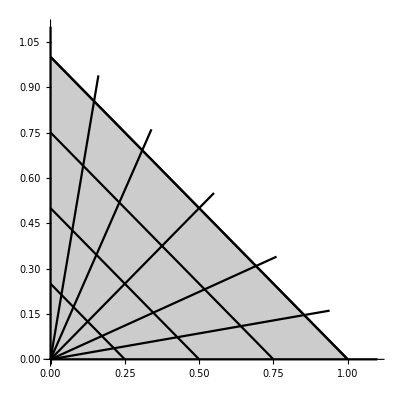

```mathematica
X[r_,theta_]:=r*Cos[theta]^2;Y[r_,theta_]:=r*Sin[theta]^2;
Quxian11=ParametricPlot[{X[1,x],Y[1,x]},{x,0,Pi/2},AxesStyle->Arrowheads[0.04],PlotStyle->Black];
Quxian12=ParametricPlot[{X[0.75,x],Y[0.75,x]},{x,0,Pi/2},AxesStyle->Arrowheads[0.04],PlotStyle->Black];
Quxian13=ParametricPlot[{X[0.5,x],Y[0.5,x]},{x,0,Pi/2},AxesStyle->Arrowheads[0.04],PlotStyle->Black];
Quxian14=ParametricPlot[{X[0.25,x],Y[0.25,x]},{x,0,Pi/2},AxesStyle->Arrowheads[0.04],PlotStyle->Black];
Quxian15=ParametricPlot[{X[0,x],Y[0,x]},{x,0,Pi/2},AxesStyle->Arrowheads[0.04],PlotStyle->Black];
Quxian20=ParametricPlot[{X[x,0],Y[x,0]},{x,0,1.1},AxesStyle->Arrowheads[0.04],PlotStyle->Black];
Quxian21=ParametricPlot[{X[x,Pi/8],Y[x,Pi/8]},{x,0,1.1},AxesStyle->Arrowheads[0.04],PlotStyle->Black];
Quxian22=ParametricPlot[{X[x,Pi/4-Pi/16],Y[x,Pi/4-Pi/16]},{x,0,1.1},AxesStyle->Arrowheads[0.04],PlotStyle->Black];
Quxian23=ParametricPlot[{X[x,Pi/4],Y[x,Pi/4]},{x,0,1.1},AxesStyle->Arrowheads[0.04],PlotStyle->Black];
Quxian24=ParametricPlot[{X[x,Pi/4+Pi/16],Y[x,Pi/4+Pi/16]},{x,0,1.1},AxesStyle->Arrowheads[0.04],PlotStyle->Black];
Quxian25=ParametricPlot[{X[x,Pi/2-Pi/8],Y[x,Pi/2-Pi/8]},{x,0,1.1},AxesStyle->Arrowheads[0.04],PlotStyle->Black];
Quxian26=ParametricPlot[{X[x,Pi/2],Y[x,Pi/2]},{x,0,1.1},AxesStyle->Arrowheads[0.04],PlotStyle->Black];
Quyu1=Plot[f[1,x],{x,0,1},Filling->Bottom,PlotRange->All,AxesStyle->Arrowheads[0.04],PlotStyle->Black,AspectRatio->1];
Show[Quyu1,Quxian11,Quxian12,Quxian13,Quxian14,Quxian15,Quxian20,Quxian21,Quxian22,Quxian23,Quxian24,Quxian25,Quxian26]
```

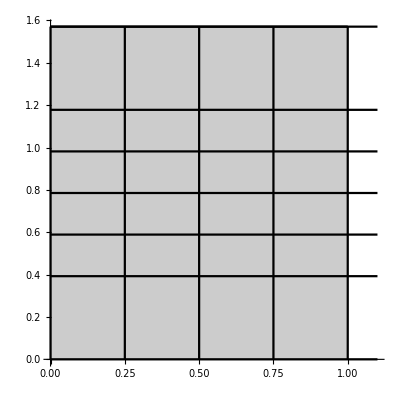

```mathematica
f[b_]:=b;g[k_]:=k;
Quxian11=ParametricPlot[{f[1],y},{y,0,Pi/2},AxesStyle->Arrowheads[0.04],PlotStyle->Black];
Quxian12=ParametricPlot[{f[0.75],y},{y,0,Pi/2},AxesStyle->Arrowheads[0.04],PlotStyle->Black];
Quxian13=ParametricPlot[{f[0.5],y},{y,0,Pi/2},AxesStyle->Arrowheads[0.04],PlotStyle->Black];
Quxian14=ParametricPlot[{f[0.25],y},{y,0,Pi/2},AxesStyle->Arrowheads[0.04],PlotStyle->Black];
Quxian15=ParametricPlot[{f[0.0],y},{y,0,Pi/2},AxesStyle->Arrowheads[0.04],PlotStyle->Black];
Quxian20=Plot[{g[0]},{x,0,1.1},AxesStyle->Arrowheads[0.04],PlotStyle->Black];
Quxian21=Plot[{g[Pi/8]},{x,0,1.1},AxesStyle->Arrowheads[0.04],PlotStyle->Black];
Quxian22=Plot[{g[Pi/4-Pi/16]},{x,0,1.1},AxesStyle->Arrowheads[0.04],PlotStyle->Black];
Quxian23=Plot[{g[Pi/4]},{x,0,1.1},AxesStyle->Arrowheads[0.04],PlotStyle->Black];
Quxian24=Plot[{g[Pi/4+Pi/16]},{x,0,1.1},AxesStyle->Arrowheads[0.04],PlotStyle->Black];
Quxian25=Plot[{g[Pi/2-Pi/8]},{x,0,1.1},AxesStyle->Arrowheads[0.04],PlotStyle->Black];Quxian26=Plot[{g[Pi/2]},{x,0,1.1},AxesStyle->Arrowheads[0.04],PlotStyle->Black];
Quyu1=Plot[Pi/2,{x,0,1},Filling->Bottom,PlotRange->All,AxesStyle->Arrowheads[0.04],PlotStyle->Black,AspectRatio->1];
Show[Quyu1,Quxian11,Quxian12,Quxian13,Quxian14,Quxian15,Quxian20,Quxian21,Quxian22,Quxian23,Quxian24,Quxian25,Quxian26]
```

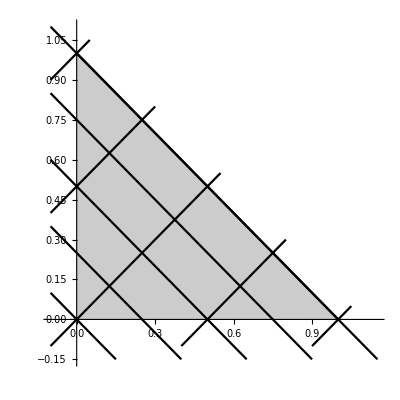

```mathematica
f[u_,x_]:=u-x;g[v_,x_]:=x-v;
Quxian11=Plot[f[1,x],{x,-0.1,1.1+0.05},AxesStyle->Arrowheads[0.04],PlotStyle->Black];
Quxian12=Plot[f[0.75,x],{x,-0.1,0.85+0.05},AxesStyle->Arrowheads[0.04],PlotStyle->Black];
Quxian13=Plot[f[0.50,x],{x,-0.1,0.60+0.05},AxesStyle->Arrowheads[0.04],PlotStyle->Black];
Quxian14=Plot[f[0.25,x],{x,-0.1,0.35+0.05},AxesStyle->Arrowheads[0.04],PlotStyle->Black];
Quxian15=Plot[f[0.0,x],{x,-0.1,0.1+0.05},AxesStyle->Arrowheads[0.04],PlotStyle->Black];
Quxian21=Plot[{g[-1,x]},{x,-0.1,0.05},AxesStyle->Arrowheads[0.04],PlotStyle->Black];
Quxian22=Plot[{g[-0.75,x]},{x,-0.1,0.35/2},AxesStyle->Arrowheads[0.04],PlotStyle->Black];
Quxian23=Plot[{g[-0.5,x]},{x,-0.1,0.6/2},AxesStyle->Arrowheads[0.04],PlotStyle->Black];
Quxian24=Plot[{g[-0.25,x]},{x,-0.1,0.85/2},AxesStyle->Arrowheads[0.04],PlotStyle->Black];
Quxian25=Plot[{g[0,x]},{x,-0.1,1.1/2},AxesStyle->Arrowheads[0.04],PlotStyle->Black];
Quxian26=Plot[{g[0.25,x]},{x,0.15,1.35/2},AxesStyle->Arrowheads[0.04],PlotStyle->Black];
Quxian27=Plot[{g[0.5,x]},{x,0.4,1.6/2},AxesStyle->Arrowheads[0.04],PlotStyle->Black];Quxian28=Plot[{g[0.75,x]},{x,0.65,1.85/2},AxesStyle->Arrowheads[0.04],PlotStyle->Black];Quxian29=Plot[{g[1,x]},{x,0.9,2.1/2},AxesStyle->Arrowheads[0.04],PlotStyle->Black];
Quyu1=Plot[f[1,x],{x,0,1},Filling->Bottom,PlotRange->All,AxesStyle->Arrowheads[0.04],PlotStyle->Black,AspectRatio->1];
Show[Quyu1,Quxian11,Quxian12,Quxian13,Quxian14,Quxian15,Quxian21,Quxian23,Quxian25,Quxian27,Quxian29]
```

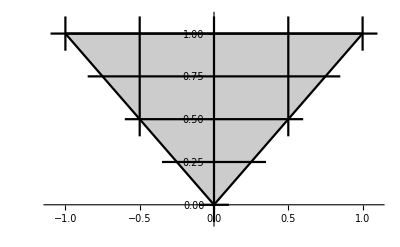

```mathematica
f[b_]:=b;g[k_]:=k;
Quxian11=Plot[{f[1]},{x,-1.1,1.1},AxesStyle->Arrowheads[0.04],PlotStyle->Black];
Quxian12=Plot[{f[0.75]},{x,-0.85,0.85},AxesStyle->Arrowheads[0.04],PlotStyle->Black];
Quxian13=Plot[{f[0.5]},{x,-0.6,0.6},AxesStyle->Arrowheads[0.04],PlotStyle->Black];
Quxian14=Plot[{f[0.25]},{x,-0.35,0.35},AxesStyle->Arrowheads[0.04],PlotStyle->Black];
Quxian15=Plot[{f[0.0]},{x,-0.1,0.1},AxesStyle->Arrowheads[0.04],PlotStyle->Black];
Quxian21=ParametricPlot[{g[-1],y},{y,0.9,1.1},AxesStyle->Arrowheads[0.04],PlotStyle->Black];
Quxian22=ParametricPlot[{g[-0.5],y},{y,0.4,1.1},AxesStyle->Arrowheads[0.04],PlotStyle->Black];
Quxian23=ParametricPlot[{g[-0],y},{y,-0.1,1.1},AxesStyle->Arrowheads[0.04],PlotStyle->Black];
Quxian24=ParametricPlot[{g[0.5],y},{y,0.4,1.1},AxesStyle->Arrowheads[0.04],PlotStyle->Black];
Quxian25=ParametricPlot[{g[1],y},{y,0.9,1.1},AxesStyle->Arrowheads[0.04],PlotStyle->Black];
Quyu1=Plot[{1,x},{x,0,1},Filling->{1->{2}},PlotRange->All,AxesStyle->Arrowheads[0.04],PlotStyle->Black];
Quyu2=Plot[{1,-x},{x,-1,0},Filling->{1->{2}},PlotRange->All,AxesStyle->Arrowheads[0.04],PlotStyle->Black];
Show[Quyu1,Quyu2,Quxian11,Quxian12,Quxian13,Quxian14,Quxian15,Quxian21,Quxian22,Quxian23,Quxian24,Quxian25]
```

```mathematica
Q=ParametricPlot3D[{r*Cos[theta],r*Sin[theta],Cos[theta]},{theta,0,2Pi},{r,0,1},PlotPoints->100,Boxed->False,Ticks->None]
```

-Graphics3D-

```mathematica
r1[t_]:=1+Sin[t];r2[t_]:=3*Cos[t];
Quxian1=ParametricPlot3D[{r1[t]Cos[t],r1[t] Sin[t],0},{t,0,2Pi},PlotStyle->{AbsoluteThickness[3],Blue},PlotPoints->30];
Quxian2=ParametricPlot3D[{r2[t] Cos[t],r2[t] Sin[t],0},{t,0,2Pi},PlotStyle->{AbsoluteThickness[3],Red},PlotPoints->30];
Quyu=ParametricPlot3D[{r Cos[t],r Sin[t],0},{t,Pi/6,Pi/2},{r,r1[t],r2[t]},PlotStyle->Yellow,Mesh->False,PlotPoints->30];
Show[Quyu,Quxian1,Quxian2,PlotRange->{{-2,3},{-2,2.2},{0,0.01}},AxesOrigin->{0,0,0},AspectRatio->0.8,Ticks->{{-1,0,1},{-1,0,1,2},{}},ViewPoint->{0,0,1},Boxed->False]
```

-Graphics3D-

```mathematica
ParametricPlot3D[{r*Cos[theta],r*Sin[theta],Cos[theta]},{theta,0,2Pi},{r,0,1},PlotPoints->100]
```

-Graphics3D-